In this analysis, we set everything in terms of the predator body size
Prey body size is then determined as a function of the predator body size: OptPreyMass = f[PredMass]

```mathematica
ClearAll["Global`*"]
```

```mathematica
namespace = StringJoin[{$HomeDirectory,"/PATH TO FOLDER/2024_PredSizeDiet"}]
```

/Users/jdyeakel/Dropbox/PostDoc/2024_PredSizeDiet

```mathematica
eqnP = (w*bPred*P*H +(1-w)* bPredSub*Sub*P) - μPred*P/.{bPred->bPred[Mp],bPredSub->bPredSub[Mp],μPred->μPred[Mp]}; 
eqnH = λ*(R/(k/2+R))*H-( σ*(1-R/k)+μ+w*bmort*P)*H/.{k->kRes,λ->λ[Mp],μ->μ[Mp],σ->σ[Mp],bmort->bmort[Mp]};
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R)))*H/.{k->kRes,λ->λ[Mp],Y->Y[Mp]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnH,0==eqnR},{P,H,R}]];
```

```mathematica
Length[LVSS]
```

7

```mathematica
Psol = P/.LVSS[[5]]
Hsol = H/.LVSS[[5]]
Rsol = R/.LVSS[[5]]
```

((8 λ[Mp])/w-(8 μ[Mp])/w+((-3 √kRes √w √α √bPred[Mp] √Y[Mp]+√(9 kRes w α bPred[Mp] Y[Mp]-16 λ[Mp] (Sub (-1+w) bPredSub[Mp]+μPred[Mp]))) (kRes w α bPred[Mp] Y[Mp]+2 (Sub (-1+w) bPredSub[Mp]+μPred[Mp]) σ[Mp]))/(√kRes w^(3/2) √α √bPred[Mp] √Y[Mp] (Sub (-1+w) bPredSub[Mp]+μPred[Mp])))/(8 bmort[Mp])

(Sub (-1+w) bPredSub[Mp]+μPred[Mp])/(w bPred[Mp])

kRes/4+(√kRes √(9 kRes w α bPred[Mp] Y[Mp]-16 λ[Mp] (Sub (-1+w) bPredSub[Mp]+μPred[Mp])))/(4 √w √α √bPred[Mp] √Y[Mp])

```mathematica
PsolNoSubsidies= Psol/.w->1
HsolNoSubsidies=Hsol/.w->1
```

(8 λ[Mp]-8 μ[Mp]+((-3 √kRes √α √bPred[Mp] √Y[Mp]+√(9 kRes α bPred[Mp] Y[Mp]-16 λ[Mp] μPred[Mp])) (kRes α bPred[Mp] Y[Mp]+2 μPred[Mp] σ[Mp]))/(√kRes √α √bPred[Mp] √Y[Mp] μPred[Mp]))/(8 bmort[Mp])

μPred[Mp]/bPred[Mp]

```mathematica
JacobianFullModel=({
{D[eqnP,P],D[eqnP,H],D[eqnP,R]},
{D[eqnH,P],D[eqnH,H],D[eqnH,R]},
{D[eqnR,P],D[eqnR,H],D[eqnR,R]}})/.{P->Psol,H->Hsol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{namespace,"/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{namespace,"/data/carnivoredensities_trimmed.csv"}],"csv"];
```

***Declare Metabolic Parameters***

```mathematica
NotebookEvaluate[StringJoin[{namespace,"/src/metabolic_constants.nb"}]];
```

***Declare Allometric Functions - SPECIFIC TO MODEL AND PERSPECTIVE***

```mathematica
NotebookEvaluate[StringJoin[{namespace,"/src/allometric_functions_predpersp.nb"}]];
```

***Declare PPMR***

```mathematica
NotebookEvaluate[StringJoin[{namespace,"/src/ppmr_primary.nb"}]];
```

***Declare Analysis Functions***

```mathematica
NotebookEvaluate[StringJoin[{namespace,"/src/analysis_functions.nb"}]];
```

Show the inputted PPMR

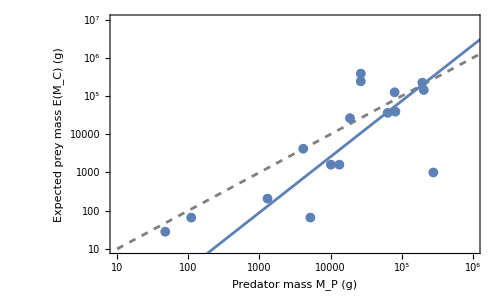

```mathematica
pstyleherb=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.1],FaceForm[Black],Disk[]}];
PPMRPlotLM = Show[{
ListLogLogPlot[ExpPreymassdata*1000,Frame->True,FrameLabel->{"Predator mass M_P (g)","Expected prey mass E(M_C) (g)"},LabelStyle->Directive[FontSize->16],PlotRange->{{10^1,1*10^6},{10^1,10^7}}],
ListLogLogPlot[Transpose[{Table[10^i,{i,1,7}],Table[10^i,{i,1,7}]}],Joined->True,PlotStyle->Directive[Gray,Dashed]],
ListLogLogPlot[ExpPreymassdata*1000,PlotMarkers->{Automatic,Medium}],
LogLogPlot[OptPreyMass[Mp],{Mp,10^1,10^7},PlotStyle->ColorData[97,1]]
},ImageSize->500,AspectRatio->3/5]
```

```mathematica
Export[StringJoin[{namespace,"/final_figures/suppfig_ppmr.pdf"}],PPMRPlotLM,"PDF"]
```

{0.0249254,0.0405269}

{-7.55073×10^-9,-1.73244×10^-9,-1.20816×10^-10}

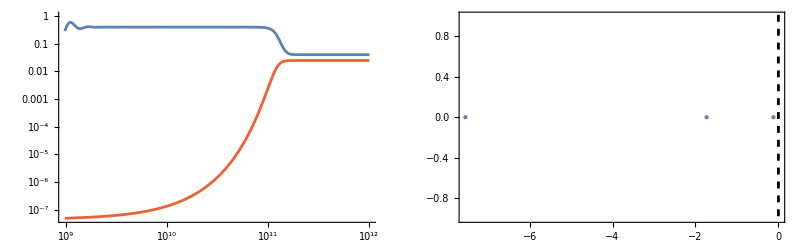

```mathematica
ndeqns=PHRSim[eqnP,eqnH,eqnR,0];
tmax = 10^12;
PredMass = 10^5;
PercentGrowthHerbivore=0.8; (*Percent with which the predator relies on Consumer 1 for food*)
PercentSubsidy =0.02;
sol = NDSolve[{
ndeqns/.{Mp->PredMass,w->PercentGrowthHerbivore,ϵ->PercentSubsidy}},
{P,H1,R},{t,tmax},Method->Automatic];
{Psol,Hsol}/.{Mp->PredMass,w->PercentGrowthHerbivore,ϵ->PercentSubsidy}
Eigs=Eigenvalues[JacobianFullModel/.{Mp->PredMass,w->PercentGrowthHerbivore,ϵ->PercentSubsidy}];
Re[Eigs]
GraphicsRow[{
LogLogPlot[Evaluate[{P[t],H1[t]}/.sol],{t,0,tmax},PlotStyle->{ColorData[97,4],ColorData[97,1]}],
Show[{ListPlot[Transpose[{Re[Eigs],Im[Eigs]}],Frame->True,PlotStyle->PointSize[Large]],ListPlot[{{0,-10},{0,10}},Joined->True,PlotStyle->Directive[{Black,Dashed}]]}]
}]
```

```mathematica
wvalues = Table[i,{i,0.01,1,0.01}];
epsilonvalues = Table[10^i,{i,-3,0,0.005}];
HsolMass = ((1/OptPreyMass[Mp])*Hsol)/.Mp->Mass;
PsolMass = ((1/Mp)*Psol)/.{Mp->Mass};
```

```mathematica
(*ThresholdsOverWEpsilonAlternate=Flatten[ParallelTable[
{thresholdsizeH,existH}= DetectThresholdSol[HsolMass/.{w->wvalues[[i]],ϵ->epsilonvalues[[j]]}];
{thresholdsizeP,existP} = DetectThresholdSol[PsolMass/.{w->wvalues[[i]],ϵ->epsilonvalues[[j]]}];
{wvalues[[i]],epsilonvalues[[j]],thresholdsizeH,thresholdsizeP, existH,existP},
{i,1,Length[wvalues]},{j,1,Length[epsilonvalues]}],1];
Export[StringJoin[{namespace,"/data/thresholdsoverwepsilon.csv"}],ThresholdsOverWEpsilonAlternate,"CSV"]*)
```

```mathematica
ThresholdsOverWEpsilonAlternateOrig=Import[StringJoin[{namespace,"/data/thresholdsoverwepsilon.csv"}]];
```

08/15/24
Reverse the w_1 axis to be w_S = 1 - w_1

```mathematica
ThresholdsOverWEpsilonAlternate = ThresholdsOverWEpsilonAlternateOrig;
ThresholdsOverWEpsilonAlternate[[All,1]] = 1- ThresholdsOverWEpsilonAlternate[[All,1]]; (*Change w1 to wS = 1 - w1*)
```

```mathematica
PreyThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],OptPreyMass[ThresholdsOverWEpsilonAlternate[[All,3]]]}];
PredThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],ThresholdsOverWEpsilonAlternate[[All,4]]}];

PreySizeGapPosAlternate=Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,3]],_?(#>5000&&#<25000&)],1];
PredSizeGapPosAlternate=Flatten[Position[PredThresholdMatrixAlternate[[All,3]],_?(#>5000&&#<25000&)],1];
PreyTMAlternate=PreyThresholdMatrixAlternate[[PreySizeGapPosAlternate,1;;2]];
PredTMAlternate=PredThresholdMatrixAlternate[[PredSizeGapPosAlternate,1;;2]];
MissingPosH = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,3]],_?(#==Missing[]&)],1];
MissingPointsH = Transpose[{ThresholdsOverWEpsilonAlternate[[MissingPosH]][[All,1]],ThresholdsOverWEpsilonAlternate[[MissingPosH]][[All,2]]}];
MissingPosP = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,4]],_?(#==Missing[]&)],1];
MissingPointsP = Transpose[{ThresholdsOverWEpsilonAlternate[[MissingPosP]][[All,1]],ThresholdsOverWEpsilonAlternate[[MissingPosP]][[All,2]]}];

UpperThreshold = 10^6.2;
LowerThreshold = 10;
UpperThresholdPosP = Flatten[Position[PredThresholdMatrixAlternate[[All,3]],_?(#>UpperThreshold||#<LowerThreshold&)],1];
PredThresholdMatrixAlternate[[UpperThresholdPosP,3]]=Missing[];
PredUpperThreshold=PredThresholdMatrixAlternate[[UpperThresholdPosP,1;;2]];

(*ExtinctPosC1 = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,5]],_?(#==0&)],1];
ExtinctPosC2= Flatten[Position[PreyThresholdMatrixAlternate[[All,3]],_?(#>10&)],1];
ExtinctPos = Flatten[Intersection[{ExtinctPosC1,ExtinctPosC2}],1];*)
ExtinctPosH1 = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,5]],_?(#==0&)],1];
ExtinctPosH2= Flatten[Position[PreyThresholdMatrixAlternate[[All,3]],_?(#<1&&#>0.0&)],1];
ExtinctPosH=Flatten[Union[{ExtinctPosH1,ExtinctPosH2}],1];
(*ExtantPosC = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,5]],_?(#>0&)],1];*)
ExtinctPointsH = Transpose[{ThresholdsOverWEpsilonAlternate[[ExtinctPosH]][[All,1]],ThresholdsOverWEpsilonAlternate[[ExtinctPosH]][[All,2]]}];
ExtinctPosP = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,6]],_?(#==0&)],1];
ExtinctPointsP = Transpose[{ThresholdsOverWEpsilonAlternate[[ExtinctPosP]][[All,1]],ThresholdsOverWEpsilonAlternate[[ExtinctPosP]][[All,2]]}];
```

```mathematica
ThresholdPlotAlternate=GraphicsRow[{
Show[{
ListContourPlot[PredThresholdMatrixAlternate,FrameLabel->{"Prop. growth from subsidy w_S","Subsidy availability S (g·m^-2)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.001,1},{1,All}},ContourStyle->None,ColorFunction->"SiennaTones",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"M_P^†",LabelStyle->{Italic,(*FontFamily->"Times New Roman",*)FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16,Black]],
(*ListLogPlot[PredThresholdMatrix[[PredSizeGapPos,1;;2]],PlotStyle->Black],*)
(*Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PredTMAlternate[[All,1]],Log@PredTMAlternate[[All,2]]}]]}],*)
(*,
Graphics[{White,Opacity[1],ConcaveHullMesh[Transpose[{MissingPointsP[[All,1]],Log@MissingPointsP[[All,2]]}],0.02,All]}]*)
Graphics[{White,ConcaveHullMesh[Transpose[{PredUpperThreshold[[All,1]],Log@PredUpperThreshold[[All,2]]}],0.02,All]}],
(*Note that Sint = 0.08 corresponds to an M_P threshold of 12 grams*)
(*LogPlot[Sint/(1-w)/.Sint->0.173(*0.08*),{w,0,1},PlotStyle->Directive[{Thickness[0.03],Dashed,Gray}]],*)
LogPlot[Sint/(1-(1-w))/.Sint->0.08,{w,0,1},PlotStyle->Directive[{Thickness[0.03],Dashed,Black}]]
}],
Show[{
ListContourPlot[PreyThresholdMatrixAlternate,FrameLabel->{"Prop. growth from subsidy w_S","Subsidy availability S (g·m^-2)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.001,1},{0.1,All}},ContourStyle->None,ColorFunction->"StarryNightColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"M_H^‡",LabelStyle->{Italic,(*FontFamily->"Times New Roman",*)FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16,Black]]
(*ListLogPlot[PreyThresholdMatrix[[PreySizeGapPos,1;;2]],PlotStyle->Black],*)
(*Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PreyTMAlternate[[All,1]],Log@PreyTMAlternate[[All,2]]}]]}],*)
(*Graphics[{White,Opacity[1],ConcaveHullMesh[Transpose[{MissingPointsC[[All,1]],Log@MissingPointsC[[All,2]]}],0.02,All]}],*)

(*,Graphics[{Gray,ConcaveHullMesh[Transpose[{ExtinctPointsC[[All,1]],Log@ExtinctPointsC[[All,2]]}],0.02,All]}]*)
,Graphics[{Gray,ConcaveHullMesh[Transpose[{PredUpperThreshold[[All,1]],Log@PredUpperThreshold[[All,2]]}],0.02,All]}]
}]
},ImageSize->850,Spacings->0]
```

-Graphics-

```mathematica
Export[StringJoin[{namespace,"/final_figures/fig_thresholdsoverwepsilon.png"}],ThresholdPlotAlternate,"PNG"]
```

What is the average small-size predator threshold when the dependence on subsidies are limited? So for example, w_S < maxvalue, with the average taken across small w_S and S?

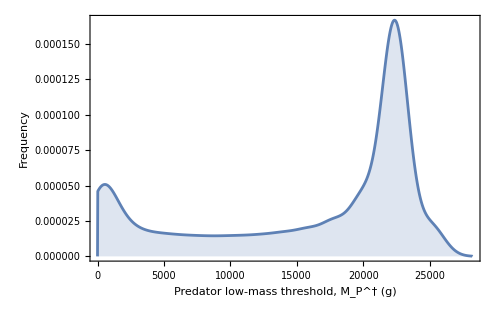

32499.1

{15770.5,7278.28,24262.8}

8492.24

```mathematica
maximumsubsidyvertebratespecialization = 0.1;(*0.05*)
SmallSizedThresholdPos = Flatten[Position[PredThresholdMatrixAlternate[[All,3]],_?(#<UpperThreshold&)],1];
PredThresholdSizes=PredThresholdMatrixAlternate[[SmallSizedThresholdPos,3]];
SpecialistPredThresholdPos = Flatten[Position[PredThresholdMatrixAlternate[[All,1]],_?(#<maximumsubsidyvertebratespecialization&)],1]; (*0.05*)
SpecialistPredThresholdSizes = PredThresholdMatrixAlternate[[Intersection[SmallSizedThresholdPos,SpecialistPredThresholdPos],3]];
PredThresholdHistPlot = SmoothHistogram[SpecialistPredThresholdSizes,1000,Frame->True,FrameLabel->{"Predator low-mass threshold, M_P^† (g)","Frequency"},PlotRange->{{0,All},All},Filling->Bottom,LabelStyle->Directive[FontSize->16,Black],ImageSize->500]
Mean[PredThresholdSizes]
{Mean[SpecialistPredThresholdSizes],Mean[SpecialistPredThresholdSizes]-StandardDeviation[SpecialistPredThresholdSizes],Mean[SpecialistPredThresholdSizes]+StandardDeviation[SpecialistPredThresholdSizes]}
StandardDeviation[SpecialistPredThresholdSizes]
```

The dominant mode is at ca. 22.4 Kg

```mathematica
Export[StringJoin[{namespace,"/final_figures/suppfig_predthresholdhist.pdf"}],PredThresholdHistPlot,"PDF"]
```

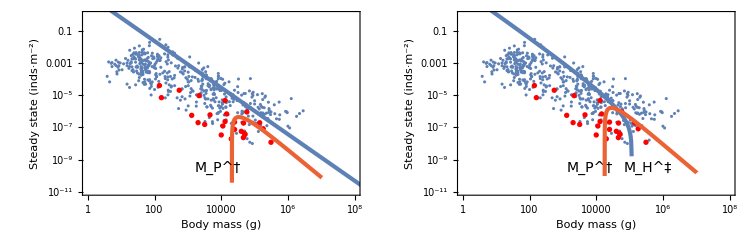

```mathematica
PercentGrowthHerbivore=1; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.08;
HerbDensityList=Table[{10^i,((1/OptPreyMass[Mp])*Hsol/.{w->PercentGrowthHerbivore,ϵ->PercentSubsidyValue})/.Mp->10^i},{i,1,8,0.01}];
HerbDensityListConsMass = Transpose[{OptPreyMass[ HerbDensityList[[All,1]]],HerbDensityList[[All,2]]}];
ThresholdPopulationPlotNoSubPredSpace=
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16,Black]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
(*LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],*)
ListLogLogPlot[HerbDensityListConsMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthHerbivore,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->14],{Log@(10^3.9),Log@(10^(-9.5))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
(*LogLogPlot[(1/OptPreyMass[Mp])*PreyDensityTheoreticalMax[OptPreyMass[Mp]]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/Mp)*PredatorDensityTheoreticalMax[Mp,OptPreyMass[Mp]]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]*)
},ImageSize->300];
PercentGrowthHerbivore=0.5; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.01;
HerbDensityList=Table[{10^i,((1/OptPreyMass[Mp])*Hsol/.{w->PercentGrowthHerbivore,ϵ->PercentSubsidyValue})/.Mp->10^i},{i,1,8,0.01}];
HerbDensityListConsMass = Transpose[{OptPreyMass[ HerbDensityList[[All,1]]],HerbDensityList[[All,2]]}];
ThresholdPopulationPlotSubPredSpace=
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16,Black]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
(*LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],*)
ListLogLogPlot[HerbDensityListConsMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthHerbivore,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->14],{Log@(10^3.8),Log@(10^(-9.5))}]}],
Graphics[{Text[Style["M_H^‡",FontSize->14],{Log@(10^5.55),Log@(10^(-9.5))}]}]
(*LogLogPlot[(1/OptPreyMass[Mp])*PreyDensityTheoreticalMax[OptPreyMass[Mp]]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/Mp)*PredatorDensityTheoreticalMax[Mp,OptPreyMass[Mp]]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]*)
},ImageSize->300];
ThresholdPopulationPlotCombPredSpace=GraphicsRow[{ThresholdPopulationPlotNoSubPredSpace,ThresholdPopulationPlotSubPredSpace},ImageSize->750,Spacings->0]
```

```mathematica
Export[StringJoin[{namespace,"/final_figures/fig_thresholdspopcomb_predpersp.png"}],ThresholdPopulationPlotCombPredSpace,"PNG"]
```

```mathematica
CombinedSubsidyFig = GraphicsColumn[{ThresholdPopulationPlotCombPredSpace,ThresholdPlotAlternate},ImageSize->1000,Spacings->-40]
```

-Graphics-